# Ideal Data

## Setup

```mathematica
<<Synthetic`
```

## Routines

```mathematica
Generate2D[D1_,{a1_,b1_},D2_,{a2_,b2_},mix_,opt:OptionsPattern[{ReferenceSampleSize->50000,"Selection"->All,"Verbose"->False}]]:=Block[{xp,yp,data,xlim,ylim,sys,gen},
xp=a1+b1 RandomVariate[D1,OptionValue[ReferenceSampleSize]];
yp=a2+b2 RandomVariate[D2,OptionValue[ReferenceSampleSize]];
gen=Transpose[{xp,yp}];
data=mix.{xp,yp};
xlim=MinMax[data[[1]]];
ylim=MinMax[data[[2]]];
data=Transpose[data];
sys=ICSTransformation[data,FilterRules[{opt},Options[ICSTransformation]]];
<|
"Generated"->gen,
"Data"->data,
"System"->sys,
"XInterval"->xlim,
"YInterval"->ylim
|>
]
```

## Testing

### 1

```mathematica
a1=3;
a2=1;
b1=0;
b2=4;
```

```mathematica
Subscript[𝔇, 1]=BetaDistribution[3,4];
Subscript[𝔇, 2]=BetaDistribution[3,6];
```

```mathematica
mix={{2,-1},{2,4}}
```

{{2,-1},{2,4}}

```mathematica
A=mix.{{a2,0},{0,b2}}
```

{{2,-4},{2,16}}

```mathematica
v1=Variance[Subscript[𝔇, 1]]
v2=Variance[Subscript[𝔇, 2]]
```

3/98

1/45

```mathematica
refCovariance=N[A.{{v1,0},{0,v2}}.Aᵀ]
```

{{0.478005,-1.29977},{-1.29977,5.81134}}

```mathematica
res=Generate2D[Subscript[𝔇, 1],{a1,a2},Subscript[𝔇, 2],{b1,b2},mix,ReferenceSampleSize->50000];
hd=HistogramDistribution[res["Data"]];
```

```mathematica
{x0,x1}=res["XInterval"]
{y0,y1}=res["YInterval"]
```

{2.86876,7.62998}

{6.62425,21.3044}

```mathematica
Table[DiscretePlot3D[Evaluate[f[hd,{x,y}]],{x,x0,x1},{y,y0,y1},ExtentSize->Full,PlotLabel->f],{f,{PDF,CDF}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
rCov=Covariance[hd]
```

{{0.488791,-1.31532},{-1.31532,6.02272}}

```mathematica
xsimu=Monitor[Table[ICSProduction[res["System"]],{k,500}],k];
xd=HistogramDistribution[xsimu];
```

```mathematica
xsimu=Monitor[Table[ICSProduction[res["System"]],{k,500}],k];
xd2=HistogramDistribution[xsimu];
```

```mathematica
Table[DiscretePlot3D[Evaluate[f[xd,{x,y}]],{x,x0,x1},{y,y0,y1},ExtentSize->Full,PlotLabel->f],{f,{PDF,CDF}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Covariance[hd]//MatrixForm
Covariance[xd]//MatrixForm
Covariance[xd2]//MatrixForm
```

(0.488791 | -1.31532
-1.31532 | 6.02272)

(0.475943 | -1.30561
-1.30561 | 6.11948)

(0.557509 | -1.53458
-1.53458 | 6.71445)

```mathematica
Histogram3D[{res["Data"],xsimu}]
```

-Graphics3D-

```mathematica
Histogram3D[{xsimu,res["Data"]}]
```

-Graphics3D-

```mathematica
ch=ConvexHullMesh[res["Data"]];
```

```mathematica
back=HighlightMesh[ch,{Style[1,{LightGray}],Style[2,LightGray]}];
```

```mathematica
tester=RegionMember[ch];
```

```mathematica
out=Function[at,
If[Not[tester[at]],at,Nothing]
]/@xsimu
```

{{7.58479,8.4042}}

```mathematica
Length[out]
```

1

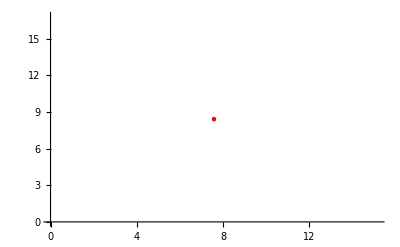

```mathematica
base=ListPlot[out,PlotStyle->{Red,PointSize[Large]},PlotRange->All]
```

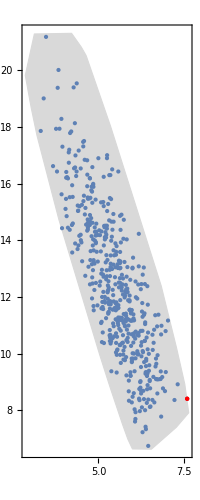

```mathematica
Show[back,ListPlot[xsimu,PlotStyle->PointSize[Medium]],base,Frame->True,FrameStyle->16]
```

### 2

```mathematica
a1=2;
a2=1;
b1=0;
b2=1;
```

```mathematica
Subscript[𝔇, 1]=BetaDistribution[3,4];
Subscript[𝔇, 2]=GammaDistribution[3,1];
```

```mathematica
mix={{2,-1},{2,4}}
```

{{2,-1},{2,4}}

```mathematica
A=mix.{{a2,0},{0,b2}}
```

{{2,-1},{2,4}}

```mathematica
v1=Variance[Subscript[𝔇, 1]]
v2=Variance[Subscript[𝔇, 2]]
```

3/98

3

```mathematica
refCovariance=N[A.{{v1,0},{0,v2}}.Aᵀ]
```

{{3.12245,-11.8776},{-11.8776,48.1224}}

```mathematica
res=Generate2D[Subscript[𝔇, 1],{a1,a2},Subscript[𝔇, 2],{b1,b2},mix,ReferenceSampleSize->50000];
hd=HistogramDistribution[res["Data"]];
```

```mathematica
{x0,x1}=res["XInterval"]
{y0,y1}=res["YInterval"]
```

{-11.8154,5.51103}

{4.45213,74.3613}

```mathematica
Table[DiscretePlot3D[Evaluate[f[hd,{x,y}]],{x,x0,x1},{y,y0,y1},ExtentSize->Full,PlotLabel->f],{f,{PDF,CDF}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
rCov=Covariance[hd]
```

{{3.28544,-11.8932},{-11.8932,52.3942}}

```mathematica
xsimu=Monitor[Table[ICSProduction[res["System"]],{k,5000}],k];
xd=HistogramDistribution[xsimu];
```

```mathematica
xsimu=Monitor[Table[ICSProduction[res["System"]],{k,5000}],k];
xd2=HistogramDistribution[xsimu];
```

```mathematica
Table[DiscretePlot3D[Evaluate[f[xd,{x,y}]],{x,x0,x1},{y,y0,y1},ExtentSize->Full,PlotLabel->f],{f,{PDF,CDF}}]
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Covariance[hd]//MatrixForm
Covariance[xd]//MatrixForm
Covariance[xd2]//MatrixForm
```

(3.28544 | -11.8932
-11.8932 | 52.3942)

(3.20689 | -12.0783
-12.0783 | 53.0985)

(3.24078 | -12.1401
-12.1401 | 53.1605)

```mathematica
Histogram3D[res["Data"]]
```

-Graphics3D-

```mathematica
xsimu=Monitor[Table[ICSProduction[res["System"]],{k,10000}],k];
```

```mathematica
Histogram3D[{xsimu,res["Data"]}]
```

-Graphics3D-

```mathematica
ch=ConvexHullMesh[res["Data"]];
```

```mathematica
back=HighlightMesh[ch,{Style[1,{LightGray}],Style[2,LightGray]}];
```

```mathematica
tester=RegionMember[ch];
```

```mathematica
out=Function[at,
If[Not[tester[at]],at,Nothing]
]/@xsimu
```

{{5.3702,5.69095},{-3.8909,35.8793},{3.56344,6.02725},{-3.5057,33.9008},{4.62228,4.46215},{-11.9959,75.1934},{5.61541,7.16613},{5.54876,5.09601},{4.74733,4.81893},{-7.20151,49.5528},{5.37649,4.67778},{-3.50979,34.515},{5.05883,5.10174}}

```mathematica
Length[out]
```

13

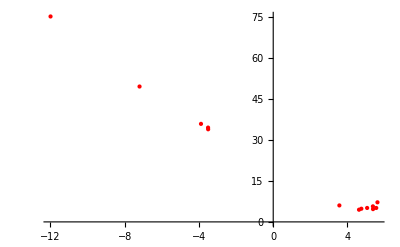

```mathematica
base=ListPlot[out,PlotStyle->{Red,PointSize[Medium]},PlotRange->All]
```

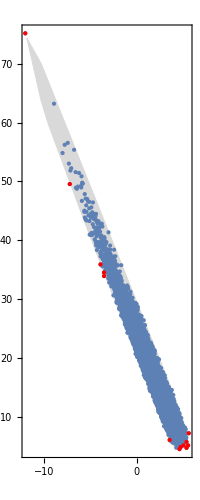

```mathematica
Show[back,ListPlot[xsimu,PlotStyle->PointSize[Medium]],base,Frame->True,FrameStyle->16]
```